# Physics 234 PS#10 (B) Eden Model: Radius of Gyration

Ziyang Gao
4/29/2018

## Section 1: What is the problem about

This problem is about investigating the Eden model and try to determine how the number of sites n in a cluster depends on its radius of gyration r. The goal is to determine the functional form of n(r), and to estimate the relevant best-fit parameters and uncertainties.

## Section 2: Statistical functions

```mathematica
ave[myList_]:=Total[myList]/Length[myList]//N;
aveSqr[myList_]:=Total[myList^2]/Length[myList]//N;
var[myList_]:=aveSqr[myList]-ave[myList]^2;
unc[myList_]:=Sqrt[var[myList]/Length[myList]];
```

## Section 3: Develop a module for generating sizeList

Code for a single growth: the code chunk below generates one time of cell growth.

```mathematica
Clear[growCells]
growCells[oldCells_]:=
Module[
{choices,oldCluster,oldBorder,newSite,nnNewSite,tempBorder,newBorder,newCluster,newCells},
	
choices={{1,0},{0,1},{-1,0},{0,-1}};
oldCluster=oldCells[[1]];
oldBorder=oldCells[[2]];
newSite=oldBorder[[RandomInteger[{1,Length[oldBorder]}]]];
newCluster=Join[oldCluster,{newSite}];
nnNewSite=Map[(#+newSite)&,choices];
tempBorder=Union[oldBorder,nnNewSite];
newBorder=Complement[tempBorder,newCluster];

newCells={newCluster,newBorder}		
];
```

A for-loop generating sizeList of 1000 times of growth:

```mathematica
oldCells={{{0,0}},{{1,0},{-1,0},{0,1},{0,-1}}};
sizeList = {};
For[i=1,i≤1000,i++,
newPic=growCells[oldCells];
clusterArea = newPic[[1]];
borderArea = Length[newPic[[2]]];
AppendTo[sizeList,clusterArea];
oldCells= {newPic[[1]],newPic[[2]]};
];
Variance[sizeList[[3]]][[1]]
sizeList[[3]]
```

11/12

(0 | 0
1 | 0
0 | -1
2 | 0)

## Section 4 : Developing the Calculation of Radius of Gyration of an existing cluster

This chunk calculates the radius of Gyration R_g based on the cells in an existing cluster, sizeList[[i]], then appends grouped R_g and number of size n into a new list relationFinal.

```mathematica
getRg[cluster_]:=
Module[
{varXY,Rg,numCell,newGroup},	
varXY=Variance[cluster];
Rg=Sqrt[varXY[[1]]+ varXY[[2]]];
numCell=Length[cluster];
newGroup={Rg,numCell}		
];
```

The code below uses getRg to generate relationFinal list and plots both the original and log version of data from relationFinal to see which plot better reflects a relationship.

```mathematica
relationFinal = {};
For[i=1,i≤1000,i++,
newGroup=getRg[sizeList[[i]]];
AppendTo[relationFinal,newGroup];
];
relationFinal[[10]]
```

{4 √(2/11),11}

From the plot below we could see that the radius of Gyration doesn’t have a linear relationship with cluster size. Now we log the two variables and see their relationship.

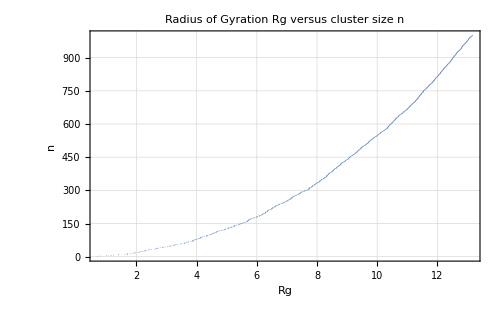

```mathematica
plot1 = ListPlot[relationFinal,PlotStyle ->{Blue[1,0,0],PointSize[0.001]},Frame -> True, FrameLabel-> {"Rg","n"},PlotRange->All,PlotLabel->Style["Radius of Gyration Rg versus cluster size n",FontFamily->"Helvetica",FontSize->12,FontWeight->"Bold"],GridLines->Automatic,ImageSize->500];
Show[plot1]
```

The logged version reflects a linear relationship: logN = 2.12 logR_g + 1.43, with a logR_gstandard error of 0.00175.

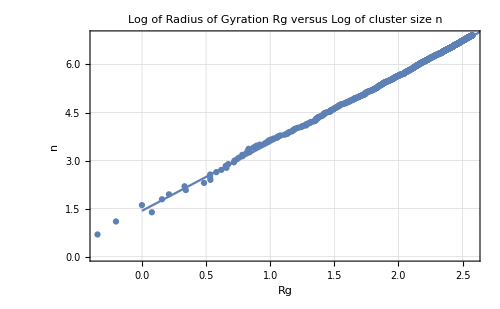

General::munfl: 0.00698145^499. is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.000682073^499. is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
1 | 1.43061 | 0.00379708 | 376.765 | 0.
x | 2.11802 | 0.00175158 | 1209.21 | 0.

2.11802 x+1.43061

{0.00379708,0.00175158}

```mathematica
logRelationFinal = Log[relationFinal];
plot2 = ListPlot[logRelationFinal,PlotStyle ->{Blue[1,0,0],PointSize[0.009]},Frame -> True, FrameLabel-> {"Rg","n"},PlotRange->All,PlotLabel->Style["Log of Radius of Gyration Rg versus Log of cluster size n",FontFamily->"Helvetica",FontSize->12,FontWeight->"Bold"],GridLines->Automatic,ImageSize->500];
model=LinearModelFit[logRelationFinal,x,x];
plot3 =Plot[model["BestFit"],{x,0,3}];
Show[plot2,plot3]
model["ParameterTable"]
model["BestFit"]
model["ParameterErrors"]
```

## Conclusion and Speculation

```mathematica
Power[Exp[1.43]]
```

4.1787

Since we get logN = 2.12 logR_g + 1.43, in the form of n(r) the function should be n(r) = 4.179 r^2.12.